```mathematica
β[r_]:=Piecewise[{{r^2+1,r≤1/2},{b,r>1/2}}]//PiecewiseExpand
u[r_]:=Piecewise[{{r^2,r≤1/2},{1/4(1-1/(8b)-1/b)+1/b(r^4/2+r^2)+C Log[2r],r>1/2}}]//PiecewiseExpand
```

```mathematica
FL=D[β[r]u[r],r]//PiecewiseExpand
Limit[FL/.b->10^-3/.C->1/10,r->1/2]
Limit[FL/.b->10^3/.C->1/10,r->1/2]
```

Piecewise[{{Indeterminate, r==1/2}, {2 (r+2 r^3), r<1/2}, {(b C+2 r^2+2 r^4)/r, True}}]

6251/5000

805/4

```mathematica
FL=D[u[r],r]//PiecewiseExpand
Limit[FL/.b->10^-3/.C->1/10,r->1/2]
Limit[FL/.b->10^3/.C->1/10,r->1/2]
```

Piecewise[{{Indeterminate, r==1/2}, {2 r, r<1/2}, {(b C+2 r^2+2 r^4)/(b r), True}}]

6251/5

161/800

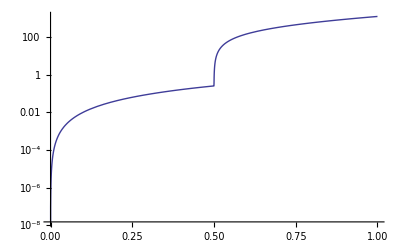

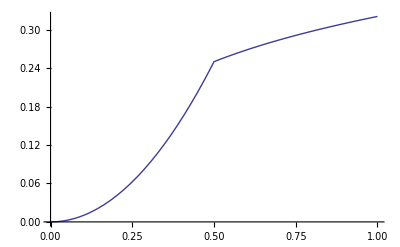

```mathematica
LogPlot[u[r]/.b->10^-3/.C->0.1,{r,0,1}]
Plot[u[r]/.b->10^3/.C->0.1,{r,0,1}]
```